```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/baryon_number_fluc/data_v2/middle_mub

```mathematica
dataall=Table[Import["../Shi_middle_mu_B/Shi_mu="<>ToString[i]<>"_m0=600.0-flag_4-51x104_VC=true.csv"],{i,800,960,5}];
```

```mathematica
n=Length[Table[i,{i,800,960,5}]]
```

33

```mathematica
dataall[[1]][[1]]
```

{T_mu,sigma,ω₀,n_B,P,e}

```mathematica
pdata=Table[Table[Table[dataall[[n1]][[j*104+i]][[5]],{i,2,105}],{j,0,50}],{n1,1,33}];
```

```mathematica
Table[Table[Export["./mub"<>ToString[800+(i-1)*5]<>"/V"<>ToString[j]<>".dat",pdata[[i]][[j]]],{i,1,33}],{j,1,51}];
```

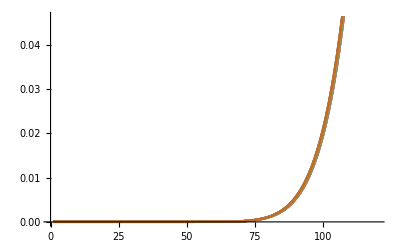

```mathematica
ListLinePlot[pdata[[1]]]
```